# Singly Periodic Scherk Surface with Enneper Ends

Ends at roots of unity. Gauss map is horizontal there. High order points with vertical normal at 0 and ∞. Additional zeroes at parameter points a. Unit circle lies on horizontal symmetry plane.

```mathematica
G[z_]:=(1-a^(-2 k))/(1-a^(2 k))(z^(k-1) (z^(2k)-a^(2k)))/(z^(2k)-1/a^(2k))
```

```mathematica
dh[z_]:=I(z^(k-1)(z^(2k)-a^(2k))(z^(2k)-1/a^(2k)))/((z^(2k)-1)^3)
```

```mathematica
phi1[z_]:=G[z]dh[z];
phi2[z_]:=1/G[z]dh[z];
```

```mathematica
ω1[z_] :=( phi2[z]-phi1[z] )/2;
ω2[z_] :=I( phi2[z]+phi1[z])/2;
ω3[z_]:=dh[z]
```

## Explicit Integrals

```mathematica
Clear[a,k]
```

```mathematica
k=1;
```

```mathematica
Integrate[{ω1[z],ω2[z],ω3[z]},z]
```

{(ⅈ (-1+a^4) z)/(2 a^2 (-1+z^2)),((3+2 a^2+3 a^4) Log[1-z]-(2 (-1+a^2)^2 z (1+z^2)+(3+2 a^2+3 a^4) (-1+z^2)^2 Log[1+z])/((-1+z^2)^2))/(16 a^2),(ⅈ ((1+6 a^2+a^4) Log[1-z]+(2 (-1+a^2)^2 z (1+z^2)-(1+6 a^2+a^4) (-1+z^2)^2 Log[1+z])/((-1+z^2)^2)))/(16 a^2)}

```mathematica
FullSimplify[%,0<a<1]
```

{(ⅈ (-1+a^4) z)/(2 a^2 (-1+z^2)),-((2 (-1+a^2)^2 z (1+z^2))/((-1+z^2)^2)+(6+4 a^2+6 a^4) ArcTanh[z])/(16 a^2),(ⅈ ((2 (-1+a^2)^2 z (1+z^2))/((-1+z^2)^2)-2 (1+6 a^2+a^4) ArcTanh[z]))/(16 a^2)}

```mathematica
G[z]
```

((1-1/a^2) (-a^2+z^2))/((1-a^2) (-1/a^2+z^2))

```mathematica
FullSimplify[%,0<a<1]
```

((a-z) (a+z))/(-1+a^2 z^2)

```mathematica
G[z_]:=((a-z) (a+z))/(-1+a^2 z^2);
```

## Wedge Domain

```mathematica
k=3;
a=.99;
rmax=4.5;
```

```mathematica
k=3;
a=.7;
rmax=1.2;
```

```mathematica
k=8;
a=.999;
rmax=5.5;
```

```mathematica
k=1;
a=.995;
rmax=6.7;
```

```mathematica
k=2;
a=.995;
rmax=4.5;
```

```mathematica
WedgeDomain[x1_Real,k_,xRng_,yRng_]:=
MeshApply[Chop[x1(1+2/(-1+I*E^#))^(2/k)]&,RectangularDomain[xRng,Pi/2.+Pi/2.*yRng]
];
```

```mathematica
ϵ=1.*^-12;
```

```mathematica
ϵ=0;
```

```mathematica
nx=10;
ny=10;
```

```mathematica
mesh=WedgeDomain[1.,2k,NRange[ϵ,rmax,nx],NRange[ϵ,1-ϵ,ny]];
```

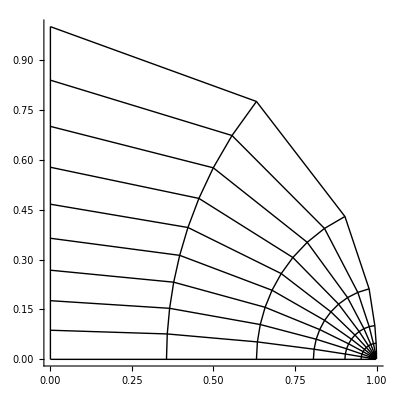

```mathematica
Show[DomainToGraphics[mesh],Axes->True]
```

## Draw Surface

```mathematica
cp=E^(Pi I/2/k);
```

```mathematica
f0[w_]:=Re[NIntegrate[{ω1[z],ω2[z],ω3[z]},{z,cp,w}]]
```

```mathematica
δ0=f0[0]
```

{0.0905041,0.454995,-0.0981779}

```mathematica
f[w_]:=f0[w]-δ0
```

```mathematica
n[w_]:=StereographicProjection[G[w]]
```

```mathematica
fr1=MeshPlot3D[{f[x+I y],n[x+I y]},{x,y},mesh];
```

```mathematica
fr2=MeshJoin[fr1,MeshRotate[fr1,StraightLine[{0,0,0},{0,1,0}]]];
```

```mathematica
fr3=MeshJoin[fr2,MeshReflect[fr2,Plane[{Cos[Pi/2/k],Sin[Pi/2/k],0},0]]];
```

```mathematica
fr4=MeshJoin@@Table[MeshRotateZ[fr3,2Pi i/k,0],{i,0,k-1}];
```

```mathematica
fr5=MeshJoin[fr4,MeshReflect[fr4,Plane[{0,0,1},δ0[[3]]]]];
```

```mathematica
fr6=MeshJoin[fr5,MeshTranslate[fr5,{0,0,4δ0[[3]]}],MeshTranslate[fr5,{0,0,-4δ0[[3]]}]];
```

```mathematica
fr6=MeshJoin[fr5,MeshTranslate[fr5,{0,0,4δ0[[3]]}],MeshTranslate[fr5,{0,0,-4δ0[[3]]}],MeshTranslate[fr5,{0,0,8δ0[[3]]}],MeshTranslate[fr5,{0,0,-8δ0[[3]]}]];
```

```mathematica
fr6=MeshJoin[fr5,MeshTranslate[fr5,{0,0,4δ0[[3]]}],MeshTranslate[fr5,{0,0,-4δ0[[3]]}]];
```

```mathematica
Show[Mesh3DToGraphicsComplex[fr6,{FaceForm[Cyan,Orange]}]]
```

-Graphics3D-

## Raytrace

Surface parameters:

```mathematica
fac=20;
```

```mathematica
nx=2fac;
ny=2fac;

mesh=WedgeDomain[1.,2k,NRange[0,rmax,nx],NRange[0,1,ny]];

fr1=MeshPlot3D[{f[x+I y],n[x+I y]},{x,y},mesh];
fr2=MeshJoin[fr1,MeshRotate[fr1,StraightLine[{0,0,0},{0,1,0}]]];
fr3=MeshJoin[fr2,MeshReflect[fr2,Plane[{Cos[Pi/2/k],Sin[Pi/2/k],0},0]]];
fr4=MeshJoin@@Table[MeshRotateZ[fr3,2Pi i/k,0],{i,0,k-1}];
fr5=MeshJoin[fr4,MeshReflect[fr4,Plane[{0,0,1},δ0[[3]]]]];
fr6=MeshJoin[fr5,MeshTranslate[fr5,{0,0,4δ0[[3]]}],MeshTranslate[fr5,{0,0,-4δ0[[3]]}]];
FR0=fr6;

nx=2;
ny=2;

mesh=WedgeDomain[1.,2k,NRange[0,rmax,nx],NRange[0,1,ny]];

fr1=MeshPlot3D[{f[x+I y],n[x+I y]},{x,y},mesh];
fr2=MeshJoin[fr1,MeshRotate[fr1,StraightLine[{0,0,0},{0,1,0}]]];
fr3=MeshJoin[fr2,MeshReflect[fr2,Plane[{Cos[Pi/2/k],Sin[Pi/2/k],0},0]]];
fr4=MeshJoin@@Table[MeshRotateZ[fr3,2Pi i/k,0],{i,0,k-1}];
fr5=MeshJoin[fr4,MeshReflect[fr4,Plane[{0,0,1},δ0[[3]]]]];
fr6=MeshJoin[fr5,MeshTranslate[fr5,{0,0,4δ0[[3]]}],MeshTranslate[fr5,{0,0,-4δ0[[3]]}]];
FR1=fr6;

nx=2fac;
ny=2;

mesh=WedgeDomain[1.,2k,NRange[0,rmax,nx],NRange[0,1,ny]];

fr1=MeshPlot3D[{f[x+I y],n[x+I y]},{x,y},mesh];
fr2=MeshJoin[fr1,MeshRotate[fr1,StraightLine[{0,0,0},{0,1,0}]]];
fr3=MeshJoin[fr2,MeshReflect[fr2,Plane[{Cos[Pi/2/k],Sin[Pi/2/k],0},0]]];
fr4=MeshJoin@@Table[MeshRotateZ[fr3,2Pi i/k,0],{i,0,k-1}];
fr5=MeshJoin[fr4,MeshReflect[fr4,Plane[{0,0,1},δ0[[3]]]]];
fr6=MeshJoin[fr5,MeshTranslate[fr5,{0,0,4δ0[[3]]}],MeshTranslate[fr5,{0,0,-4δ0[[3]]}]];
FR2=fr6;


nx=2;
ny=2fac;

mesh=WedgeDomain[1.,2k,NRange[0,rmax,nx],NRange[0,1,ny]];

fr1=MeshPlot3D[{f[x+I y],n[x+I y]},{x,y},mesh];
fr2=MeshJoin[fr1,MeshRotate[fr1,StraightLine[{0,0,0},{0,1,0}]]];
fr3=MeshJoin[fr2,MeshReflect[fr2,Plane[{Cos[Pi/2/k],Sin[Pi/2/k],0},0]]];
fr4=MeshJoin@@Table[MeshRotateZ[fr3,2Pi i/k,0],{i,0,k-1}];
fr5=MeshJoin[fr4,MeshReflect[fr4,Plane[{0,0,1},δ0[[3]]]]];
fr6=MeshJoin[fr5,MeshTranslate[fr5,{0,0,4δ0[[3]]}],MeshTranslate[fr5,{0,0,-4δ0[[3]]}]];
FR3=fr6;


PoVExport["dummy",FR0,FR1,FR3,FR2];
```